# Kerr photon regions by He-Xu Zhang

## --------------------务必使用12.1及以上版本打开

```mathematica
Δ[M_,a_]:=(√(x^2+z^2)-M)^2-2 M (√(x^2+z^2)-M)+a^2;
gtt[M_,a_]:=(√(x^2+z^2)-M)^2-2 M (√(x^2+z^2)-M)+a^2 z^2/(x^2+z^2);
```

```mathematica
PhReigon[M_,a_]:=(4 (√(x^2+z^2)-M) ((√(x^2+z^2)-M)^2-2 M (√(x^2+z^2)-M)+a^2)-((√(x^2+z^2)-M)^2+a^2 z^2/(x^2+z^2)) 2 ((√(x^2+z^2)-M)-M))^2-16 a^2 (√(x^2+z^2)-M)^2 ((√(x^2+z^2)-M)^2-2 M (√(x^2+z^2)-M)+a^2) x^2/(x^2+z^2);
```

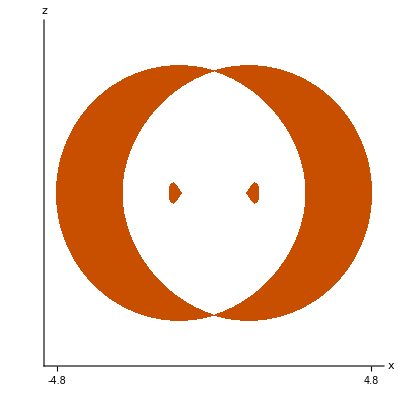

```mathematica
(*RegionPlot[PhReigon[1,0.8]<0&&x^2+z^2>1,{x,-5,5},{z,-5,5},BoundaryStyle->None,PlotStyle->RGBColor[0.788235,0.309803,0],PlotPoints->50,Axes->True,AxesLabel->{x,z},AxesStyle->Thickness[0.004],Ticks->{{-4.8,4.8},None},TicksStyle->Black,Frame->None]*)
```

```mathematica
(*Δr[M_,a_,r_]:=r^2-2 M r+a^2;
NSolve[2 r Δr[1,0.8,r] D[Δr[1,0.8,r],r]+r^2 (D[Δr[1,0.8,r],r])^2-2 r^2 Δr[1,0.8,r] D[Δr[1,0.8,r],{r,2}]==0,r]*)
```

{{r→0.},{r→0.288621},{r→1.35569-0.616072 ⅈ},{r→1.35569+0.616072 ⅈ}}

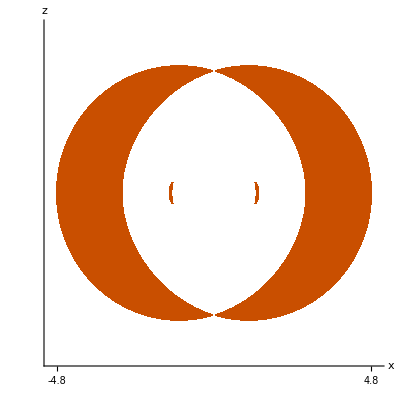

```mathematica
aa=RegionPlot[PhReigon[1,0.8]<0&&x^2+z^2>(1.288621)^2,{x,-5,5},{z,-5,5},BoundaryStyle->None,PlotStyle->RGBColor[0.788235,0.309803,0],PlotPoints->200,Axes->True,AxesLabel->{x,z},AxesStyle->Thickness[0.004],Ticks->{{-4.8,4.8},None},TicksStyle->Black,Frame->None]
```

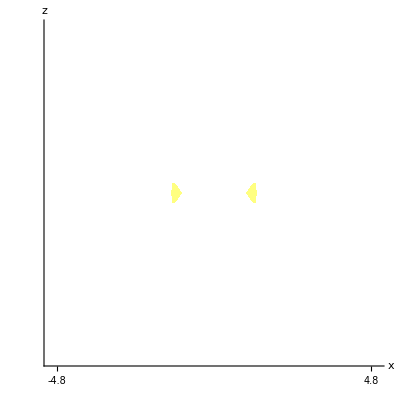

```mathematica
bb=RegionPlot[PhReigon[1,0.8]<0&&x^2+z^2<(1.288621)^2&&x^2+z^2>1,{x,-5,5},{z,-5,5},BoundaryStyle->None,PlotStyle->RGBColor[1,1,0.501960],PlotPoints->100,Axes->True,AxesLabel->{x,z},AxesStyle->Thickness[0.004],Ticks->{{-4.8,4.8},None},TicksStyle->Black,Frame->None]
```

```mathematica
PhReigon1[M_,a_]:=(4 M Log[(√(x^2+z^2))/M] ((M Log[(√(x^2+z^2))/M])^2-2 M (M Log[(√(x^2+z^2))/M])+a^2)-((M Log[(√(x^2+z^2))/M])^2+a^2 z^2/(x^2+z^2)) 2 ((M Log[(√(x^2+z^2))/M])-M))^2-16 a^2 (M Log[(√(x^2+z^2))/M])^2 ((M Log[(√(x^2+z^2))/M])^2-2 M (M Log[(√(x^2+z^2))/M])+a^2) x^2/(x^2+z^2);
(*cc=RegionPlot[PhReigon1[1,0.8]<0&&x^2+z^2>1&&x^2+z^2<(1.288621)^2,{x,-5,5},{z,-5,5},BoundaryStyle->None,PlotStyle->RGBColor[1,1,0.501960],PlotPoints->200,Axes->True,AxesLabel->{x,z},AxesStyle->Thickness[0.004],Ticks->{{-4.8,4.8},None},TicksStyle->Black,Frame->None]*)
```

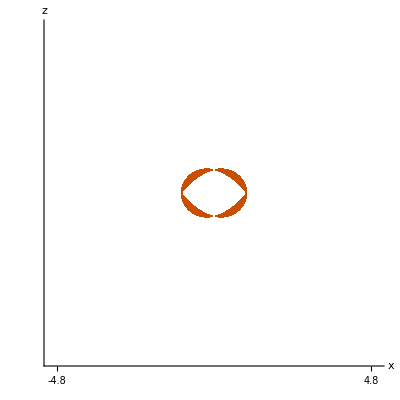

```mathematica
dd=RegionPlot[PhReigon1[1,0.8]<0&&x^2+z^2<1,{x,-5,5},{z,-5,5},BoundaryStyle->None,PlotStyle->RGBColor[0.788235,0.309803,0],PlotPoints->200,Axes->True,AxesLabel->{x,z},AxesStyle->Thickness[0.004],Ticks->{{-4.8,4.8},None},TicksStyle->Black,Frame->None]
```

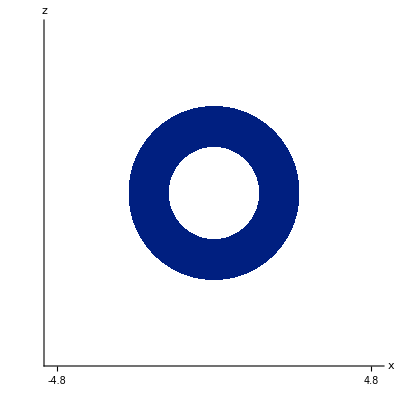

```mathematica
ee=RegionPlot[Δ[1,0.8]<0,{x,-5,5},{z,-5,5},BoundaryStyle->None,PlotStyle->RGBColor[0,0.121568,0.501960],PlotPoints->100,Axes->True,AxesLabel->{x,z},AxesStyle->Thickness[0.004],Ticks->{{-4.8,4.8},None},TicksStyle->Black,Frame->None]
```

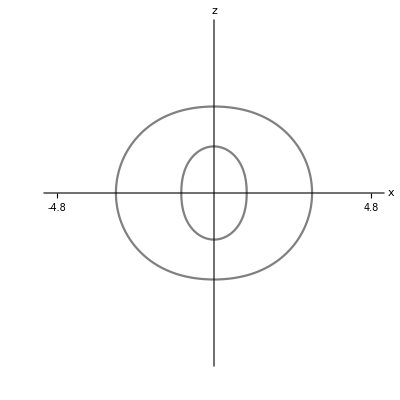

```mathematica
ff=ContourPlot[gtt[1,0.8]==0,{x,-5,5},{z,-5,5},ContourStyle->RGBColor[0.501960,0.501960,0.501960],PlotPoints->50,Axes->True,AxesLabel->{x,z},AxesStyle->Thickness[0.004],Ticks->{{-4.8,4.8},None},TicksStyle->Black,Frame->None]
```

```mathematica
gϕϕ[M_,a_]:=((M Log[(√(x^2+z^2))/M])^2+a^2)^2-a^2 ((M Log[(√(x^2+z^2))/M])^2-2 M (M Log[(√(x^2+z^2))/M])+a^2) x^2/(x^2+z^2);
gg=RegionPlot[gϕϕ[1,0.8]<0,{x,-5,5},{z,-5,5},BoundaryStyle->RGBColor[0.6,0.69019,1],PlotStyle->{RGBColor[0.6,0.69019,1],HatchFilling[-π/4]},PlotPoints->50,Axes->True,AxesLabel->{x,z},AxesStyle->Thickness[0.004],Ticks->{{-4.8,4.8},None},TicksStyle->Black,Frame->None]
```

-Graphics-

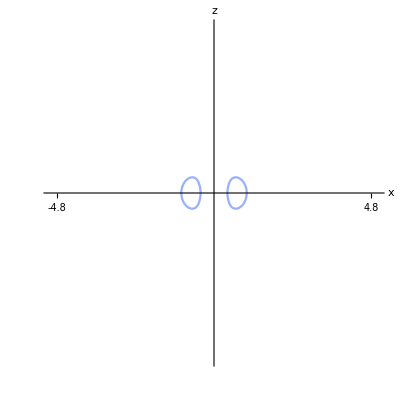

```mathematica
(*gg0=ContourPlot[gϕϕ[1,0.8]==0,{x,-5,5},{z,-5,5},ContourStyle->RGBColor[0.6,0.69019,1],PlotPoints->50,Axes->True,AxesLabel->{x,z},AxesStyle->Thickness[0.004],Ticks->{{-4.8,4.8},None},TicksStyle->Black,Frame->None]*)
```

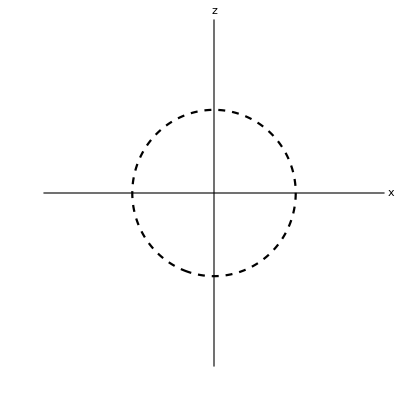

```mathematica
hh=ContourPlot[x^2+z^2==1,{x,-2,2},{z,-2,2},ContourStyle->{Dashed,Black},PlotPoints->50,Axes->True,AxesLabel->{x,z},AxesStyle->Thickness[0.004],Ticks->{{-4.8,4.8},None},TicksStyle->Black,Frame->None]
```

```mathematica
(*Show[aa,bb,dd,ee,ff,gg,hh]*)
```

-Graphics-

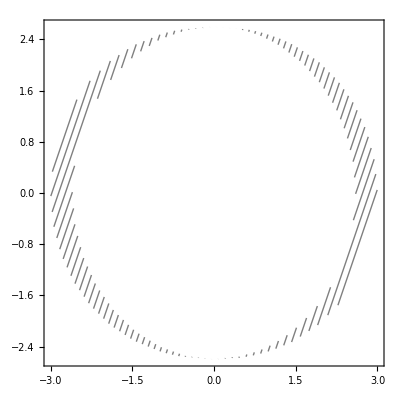

```mathematica
(*reg1=ImplicitRegion[Δ[1,0.8]>0&&gtt[1,0.8]<0&&x^2+z^2>2^2,{x,z}];
reg11=DiscretizeRegion[reg1,{{-5,5},{-5,5}}];
ii0=ContourPlot[2.5 x-z,{x,z}∈reg11,ContourShading->None,Contours->50,ContourStyle->RGBColor[0.501960,0.501960,0.501960]]*)
```

```mathematica
ii=RegionPlot[Δ[1,0.8]>0&&gtt[1,0.8]<0&&x^2+z^2>2^2,{x,-5,5},{z,-5,5},BoundaryStyle->None,PlotStyle->{RGBColor[0.501960,0.501960,0.501960],HatchFilling[π/4]}]
```

-Graphics-

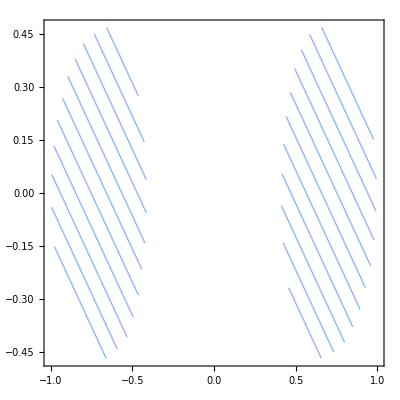

```mathematica
(*reg2=ImplicitRegion[gϕϕ[1,0.8]<0,{x,z}];
reg22=DiscretizeRegion[reg2,{{-5,5},{-5,5}}];
jj=ContourPlot[1 x+z,{x,z}∈reg22,ContourShading->None,Contours->25,ContourStyle->RGBColor[0.6,0.69019,1]]*)
```

```mathematica
kk=Graphics[{{PointSize[Large],Point[{-1,0}]},{PointSize[Large],Point[{1,0}]}}](*画龙点睛，最后画奇点并把它放在Show的最后面也是防止它被其他图形盖住*)
```

-Graphics-

```mathematica
Show[aa,bb,dd,ee,ff,gg,hh,ii,kk]
```

-Graphics-